x+x/(x^2+y^2)
y-y/(x^2+y^2)

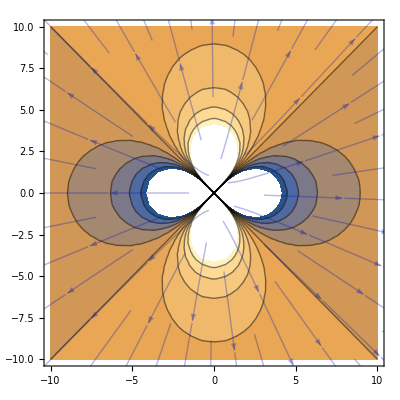
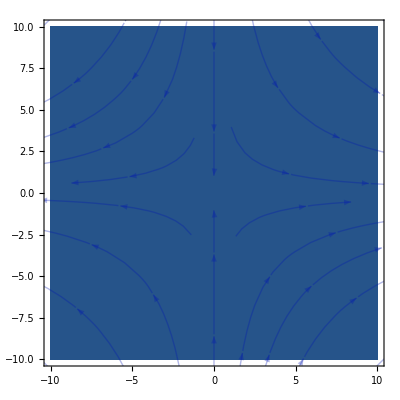
{{(1-(2 x^2)/((x^2+y^2)^2)+1/(x^2+y^2) | -(2 x y)/((x^2+y^2)^2)
(2 x y)/((x^2+y^2)^2) | 1+(2 y^2)/((x^2+y^2)^2)-1/(x^2+y^2))
{0,0}
{div,2-(2 x^2)/((x^2+y^2)^2)+(2 y^2)/((x^2+y^2)^2),curl,(4 x y)/((x^2+y^2)^2)}
-Graphics-
-Graphics3D-
-Graphics3D-},{(1-(2 x^2)/((x^2+y^2)^2)+1/(x^2+y^2) | -(2 x y)/((x^2+y^2)^2)
-(2 x y)/((x^2+y^2)^2) | -1-(2 y^2)/((x^2+y^2)^2)+1/(x^2+y^2))
{2-(2 x^2)/((x^2+y^2)^2)+(2 y^2)/((x^2+y^2)^2),-(4 x y)/((x^2+y^2)^2)}
{div,0,curl,0}
-Graphics-
-Graphics3D-
-Graphics3D-}}

```mathematica
ClearAll[Evaluate[Context[]<>"*"]];


PlotDivCurl[u_,v_]:=Module[
{ux,uy,vx,vy,matrix,div,curl,start,end,len},

{
({{ux, uy}, {vx, vy}})=D[{u,v},{{x,y}}];
matrix={ux-vy,vx+uy}//Simplify;

div=Div[{u,v},{x,y}]//Simplify;
curl=Curl[{u,v},{x,y}]//Simplify;


start=-30;end=-start;len=end;
{({{ux, uy}, {vx, vy}})//MatrixForm,matrix,{"div",div,"curl",curl},
Show[
(*ContourPlot[div,{x,-10,10},{y,-10,10}],*)
StreamPlot[{u,v},{x,start,end},{y,start,end},StreamStyle->{Opacity[0.3]}]
],
Plot3D[div,{x,start,end},{y,start,end},PlotLegends->Automatic],
Plot3D[curl,{x,start,end},{y,start,end},PlotLegends->Automatic]
}//Column
}]

z=(x+I*y);
fz= z+1/z;

{u,v}={Re[fz],Im[fz]}//ComplexExpand;
{u,v}//Column
{
PlotDivCurl[u,v],
(*复函数的复共轭向量场没有旋度和散度. https://wuli.wiki/online/HolHar.html
当计算复变函数积分时就是再变相的实数里积他的旋度散度都为0（柯西积分公式）
	原因是（柯西-黎曼公式）。-本质是 克里斯托弗符号 对称？
*)
PlotDivCurl[u,-v]
}
```